# Figures 1, 2 and 3

Copyright (c) 2019 Raj Saha (rsaha@bates.edu) and Meredith Greer (mgreer@bates.edu)

Permission is hereby granted, free of charge, to any person obtaining a copy
of this software and associated documentation files (the "Software"), to deal
in the Software without restriction, including without limitation the rights
to use, copy, modify, merge, publish, distribute, sub-license, and/or sell
copies of the Software, and to permit persons to whom the Software is
furnished to do so, subject to the following conditions : The above copyright notice and this permission notice shall be included in all copies or substantial portions of the Software.

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Japan Hida

```mathematica
label="HidaJapan";
yMAX=82;
startyear=1771;
```

```mathematica
parentpath="";
spdeathstotal=Import[StringJoin[parentpath,"smallpox_totaldeaths_",label,".dat"]]//Flatten;
maxspdeathstotal=spdeathstotal//Max;
spdeathsfactor=1;
spdeathstotal=spdeathstotal/.x_->{x/spdeathsfactor};
spdeathstotal//Max//ScientificForm;
```

```mathematica
datalength=spdeathstotal//Flatten//Length;
```

```mathematica
expfactor=Log10[spdeathsfactor];
```

```mathematica
waveletSpectra2D=Import[StringJoin[parentpath,"wav_spectra2D_",label,".dat"]];
waveletglobal=Import[StringJoin[parentpath,"wav_global_",label,".dat"]];
maxwaveletglobal=waveletglobal⟦;;,3⟧//Max;
waveletglobal⟦;;,2⟧//Max;
powerfactor=10^Floor[Log10[maxwaveletglobal]];
waveletglobal=waveletglobal/.{x_,y_,z_}->{x,y/powerfactor,z/powerfactor};
waveletcoi=Import[StringJoin[parentpath,"wav_coi_",label,".dat"]];
fftspectra=Import[StringJoin[parentpath,"fft_spectra_",label,".dat"]];
maxfftspectra=fftspectra⟦;;,2⟧//Max;
```

```mathematica
fftfactor=1 10^2; (* Japan *)

fftspectra=fftspectra/.{x_,y_}->{x,y/fftfactor};
```

```mathematica
yticks=Table[{i,2^i},{i,2,5,1}]
```

{{2,4},{3,8},{4,16},{5,32}}

```mathematica
imgheight=300;
imgpadding=50;
aspecrat=1/3.5;
```

```mathematica
yticsspdeaths=Table[i,{i,0,IntegerPart[Max[spdeathstotal]]}];
```

```mathematica
plotspdeaths=ListStepPlot[spdeathstotal,
Frame->True,AspectRatio->aspecrat,ImagePadding->imgpadding,ImageSize->{Automatic,imgheight},
PlotStyle->RGBColor["#2F4858"],
FrameLabel->{None,"Smallpox Deaths"},
PlotRange->{{1, datalength-1},All}
];
```

```mathematica
plotspectra2D=ListContourPlot[waveletSpectra2D,
ColorFunctionScaling-> False, ColorFunction->ColorData[{"CMYKColors",{-4.5,6.5}}],
Contours->35,ContourLabels->False,InterpolationOrder->5,
FrameTicks->{{yticks,None},{Automatic,None}},
PlotRange->{{1,yMAX-1},{1.4,5},{-22,6.5}},
ContourStyle->None,AspectRatio->aspecrat
];
```

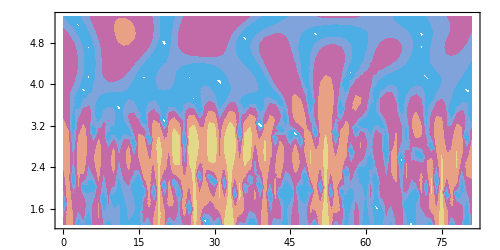

```mathematica
ListContourPlot[waveletSpectra2D,ContourStyle->None,ColorFunctionScaling-> False, ColorFunction->ColorData[{"CMYKColors",{-4.5,6.5}}],ImageSize->500,AspectRatio->1/2,InterpolationOrder->1]
```

```mathematica
waveletcoiYear=Table[{i,waveletcoi⟦i+1⟧⟦1⟧},{i,1,yMAX}];
```

```mathematica
plotcoi=ListLinePlot[waveletcoiYear,Filling->Top,FillingStyle->Directive[Opacity[0.5],White],PlotRange->{{1,yMAX},{1.4,5}}];
```

```mathematica
plotspectracomb=Show[plotspectra2D,plotcoi,FrameLabel->{StringJoin["Years, starting ",ToString[startyear]],"Period (years)"},ImageSize->{Automatic,imgheight},ImagePadding->imgpadding,PlotRange->{{1, datalength-1},{1.4,5}}];
```

```mathematica
powerMAX=17;
xticsGlobalSpectra=Table[x,{x,0,powerMAX,IntegerPart[powerMAX/3]}];

plotglobal=
Show[
ListLinePlot[{fftspectra⟦;;,{2,1}⟧,waveletglobal⟦;;,{2,1}⟧,waveletglobal⟦;;,{3,1}⟧},
Frame->True,FrameTicks->{{yticks,None},{xticsGlobalSpectra,None}},
PlotRange->{{0,17},{1.4,5}},
FrameLabel->{"Power (x 10^3)",None},
PlotStyle->{{RGBColor["#A9B4C2"],Opacity[0.5]},RGBColor[0.368417,0.506779,0.709798],{Dashed,Gray}},
ImageSize->{imgheight,imgheight},ImagePadding->imgpadding,
AspectRatio->1],

(* Hida *)
Graphics[Text[Style["6.6 y",FontSize->12,Black],{9.7,2.5}]]
];
```

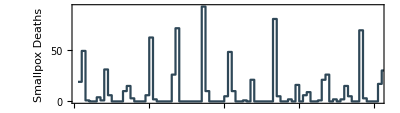
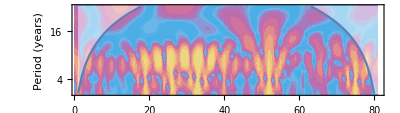
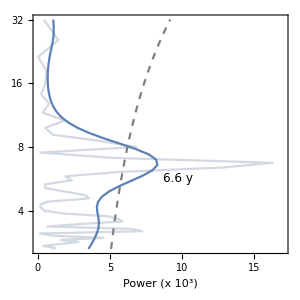
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
plotALL=Grid[{
{plotspdeaths},
{plotspectracomb,plotglobal}
},
Spacings->{-5,-5}
]
```

#### WaveletScalogram and BarLegend

```mathematica
spdeaths=Import["/Users/raj/Documents/research/smallpox/__summer_2018/_data/Japan Hida/spdeaths.dat"];
```

```mathematica
spdeaths=spdeaths⟦1;;,2⟧
```

{19,49,1,0,0,4,1,31,6,0,0,0,10,15,3,0,0,0,6,62,2,0,0,0,0,26,71,0,0,0,0,0,0,92,10,0,0,0,0,5,48,10,0,0,1,0,21,0,0,0,0,0,80,5,0,0,2,0,16,0,6,9,0,0,1,21,26,0,2,0,2,15,5,0,0,69,3,0,0,0,17,30}

```mathematica
cwd=ContinuousWaveletTransform[spdeaths]
```

ContinuousWaveletData[<<CWT>>, <5,4>, {82}]

```mathematica
WaveletScalogram[cwd,ColorFunctionScaling-> False, ColorFunction->ColorData[{"CMYKColors",{0,75}}]]
```

-Graphics-

```mathematica
BarLegend[{"CMYKColors",{0,70}},Table[i,{i,0,70,10}]]
```

## British India

```mathematica
label="BritishIndia";
yMAX=51;
startyear=1870;
```

```mathematica
parentpath="";
spdeathstotal=Import[StringJoin[parentpath,"smallpox_totaldeaths_",label,".dat"]]//Flatten;
maxspdeathstotal=spdeathstotal//Max;

spdeathsfactor=10^Floor[Log10[maxspdeathstotal]];

spdeathstotal=spdeathstotal/.x_->{x/spdeathsfactor};
spdeathstotal//Max//ScientificForm;
```

```mathematica
datalength=spdeathstotal//Flatten//Length;
```

```mathematica
expfactor=Log10[spdeathsfactor];
```

```mathematica
waveletSpectra2D=Import[StringJoin[parentpath,"wav_spectra2D_",label,".dat"]];
waveletglobal=Import[StringJoin[parentpath,"wav_global_",label,".dat"]];
maxwaveletglobal=waveletglobal⟦;;,3⟧//Max;
waveletglobal⟦;;,2⟧//Max;
powerfactor=10^Floor[Log10[maxwaveletglobal]];
waveletglobal=waveletglobal/.{x_,y_,z_}->{x,y/powerfactor,z/powerfactor};
waveletcoi=Import[StringJoin[parentpath,"wav_coi_",label,".dat"]];
fftspectra=Import[StringJoin[parentpath,"fft_spectra_",label,".dat"]];
maxfftspectra=fftspectra⟦;;,2⟧//Max;
```

```mathematica
fftfactor=1 10^10; 
fftspectra=fftspectra/.{x_,y_}->{x,y/fftfactor};
```

```mathematica
yticks=Table[{i,2^i},{i,2,5,1}];
```

```mathematica
imgheight=300;
imgpadding=50;
aspecrat=1/3.5;
```

```mathematica
yticsspdeaths=Table[i,{i,0,IntegerPart[Max[spdeathstotal]]}];
```

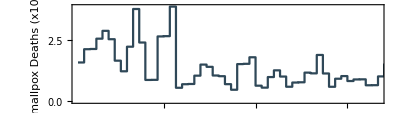

```mathematica
plotspdeaths=ListStepPlot[spdeathstotal,
Frame->True,AspectRatio->aspecrat,ImagePadding->imgpadding,ImageSize->{Automatic,imgheight},
PlotStyle->RGBColor["#2F4858"],
FrameLabel->{None,"Smallpox Deaths (x10^5)"},
PlotRange->{{1, datalength-1},All}
]
```

```mathematica
plotspectra2D=ListContourPlot[waveletSpectra2D,
ColorFunctionScaling-> False, ColorFunction->ColorData[{"CMYKColors",{-4.5,6.5}}],
Contours->35,ContourLabels->False,InterpolationOrder->5,
FrameTicks->{{yticks,None},{Automatic,None}},
PlotRange->{{1,yMAX-1},{1.4,5},{-22,6.5}},
ContourStyle->None,AspectRatio->aspecrat
];
```

```mathematica
waveletcoiYear=Table[{i,waveletcoi⟦i+1⟧⟦1⟧},{i,1,yMAX}];
```

```mathematica
plotcoi=ListLinePlot[waveletcoiYear,Filling->Top,FillingStyle->Directive[Opacity[0.5],White],PlotRange->{{1,yMAX},{1.4,5}}];
```

```mathematica
plotspectracomb=Show[plotspectra2D,plotcoi,FrameLabel->{StringJoin["Years, starting ",ToString[startyear]],"Period (years)"},ImageSize->{Automatic,imgheight},ImagePadding->imgpadding,PlotRange->{{1, datalength-1},{1.4,5}}];
```

```mathematica
powerMAX=17;
xticsGlobalSpectra=Table[x,{x,0,powerMAX,IntegerPart[powerMAX/3]}];

plotglobal=
Show[
ListLinePlot[{fftspectra⟦;;,{2,1}⟧,waveletglobal⟦;;,{2,1}⟧,waveletglobal⟦;;,{3,1}⟧},
Frame->True,FrameTicks->{{yticks,None},{xticsGlobalSpectra,None}},

PlotRange->{{0,3.5},{1.4,5}},
FrameLabel->{"Power (x 10^10)",None},

PlotStyle->{{RGBColor["#A9B4C2"],Opacity[0.5]},RGBColor[0.368417,0.506779,0.709798],{Dashed,Gray}},
ImageSize->{imgheight,imgheight},ImagePadding->imgpadding,
AspectRatio->1],

Graphics[Text[Style["5.5 y",FontSize->12,Black],{1.5,2.2}]]
];
```

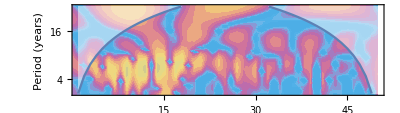
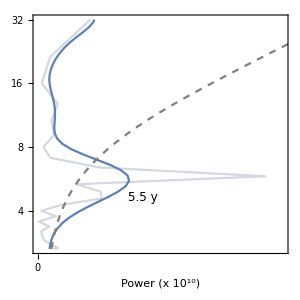
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
plotALL=Grid[{
{plotspdeaths},
{plotspectracomb,plotglobal}
},
Spacings->{-5,-5}
]
```

## Sweden

```mathematica
label="Sweden";
yMAX=27;
startyear=1774;
peakperiod=5.2;
```

```mathematica
parentpath="";
spdeathstotal=Import[StringJoin[parentpath,"smallpox_totaldeaths_",label,".dat"]]//Flatten;
maxspdeathstotal=spdeathstotal//Max;
spdeathsfactor=10^Floor[Log10[maxspdeathstotal]];

spdeathstotal=spdeathstotal/.x_->{x/spdeathsfactor};
spdeathstotal//Max//ScientificForm;
```

```mathematica
datalength=spdeathstotal//Flatten//Length;
```

```mathematica
expfactor=Log10[spdeathsfactor];
```

```mathematica
waveletSpectra2D=Import[StringJoin[parentpath,"wav_spectra2D_",label,".dat"]];
waveletglobal=Import[StringJoin[parentpath,"wav_global_",label,".dat"]];
maxwaveletglobal=waveletglobal⟦;;,3⟧//Max;
waveletglobal⟦;;,2⟧//Max;
powerfactor=10^Floor[Log10[maxwaveletglobal]];
waveletglobal=waveletglobal/.{x_,y_,z_}->{x,y/powerfactor,z/powerfactor};
waveletcoi=Import[StringJoin[parentpath,"wav_coi_",label,".dat"]];
fftspectra=Import[StringJoin[parentpath,"fft_spectra_",label,".dat"]];
maxfftspectra=fftspectra⟦;;,2⟧//Max;
```

```mathematica
fftfactor=1 10^7; (* Sweden *)
fftspectra=fftspectra/.{x_,y_}->{x,y/fftfactor};
```

```mathematica
yticks=Table[{i,2^i},{i,2,5,1}];
```

```mathematica
imgheight=300;
imgpadding=50;
aspecrat=1/3.5;
```

```mathematica
yticsspdeaths=Table[i,{i,0,IntegerPart[Max[spdeathstotal]]}];
```

```mathematica
plotspdeaths=ListStepPlot[spdeathstotal,
Frame->True,AspectRatio->aspecrat,ImagePadding->imgpadding,ImageSize->{Automatic,imgheight},
PlotStyle->RGBColor["#2F4858"],
FrameLabel->{None,"Smallpox Deaths (x10^4)"},
PlotRange->{{1, datalength-1},All}
];
```

```mathematica
plotspectra2D=ListContourPlot[waveletSpectra2D,
ColorFunctionScaling-> False, ColorFunction->ColorData[{"CMYKColors",{-4.5,6.5}}],
Contours->35,ContourLabels->False,InterpolationOrder->5,
FrameTicks->{{yticks,None},{Automatic,None}},
PlotRange->{{1,yMAX-1},{1.4,5},{-22,6.5}},
ContourStyle->None,AspectRatio->aspecrat
];
```

```mathematica
waveletcoiYear=Table[{i,waveletcoi⟦i+1⟧⟦1⟧},{i,1,yMAX}];
```

```mathematica
plotcoi=ListLinePlot[waveletcoiYear,Filling->Top,FillingStyle->Directive[Opacity[0.5],White],PlotRange->{{1,yMAX},{1.4,5}}];
```

```mathematica
plotspectracomb=Show[plotspectra2D,plotcoi,FrameLabel->{StringJoin["Years, starting ",ToString[startyear]],"Period (years)"},ImageSize->{Automatic,imgheight},ImagePadding->imgpadding,PlotRange->{{1, datalength-1},{1.4,5}}];
```

```mathematica
powerMAX=17;
xticsGlobalSpectra=Table[x,{x,0,powerMAX,IntegerPart[powerMAX/3]}];
plotglobal=
Show[
ListLinePlot[{fftspectra⟦;;,{2,1}⟧,waveletglobal⟦;;,{2,1}⟧,waveletglobal⟦;;,{3,1}⟧},
Frame->True,FrameTicks->{{yticks,None},{xticsGlobalSpectra,None}},
PlotRange->{{0,10},{1.4,5}},
FrameLabel->{"Power (x 10^7)",None},
PlotStyle->{{RGBColor["#A9B4C2"],Opacity[0.5]},RGBColor[0.368417,0.506779,0.709798],{Dashed,Gray}},
ImageSize->{imgheight,imgheight},ImagePadding->imgpadding,
AspectRatio->1],

Graphics[Text[Style["5.2 y",FontSize->12,Black],{4.2,2.15}]]
];
```

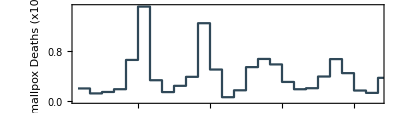
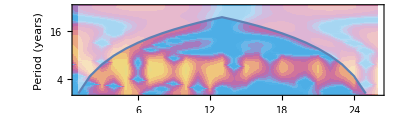
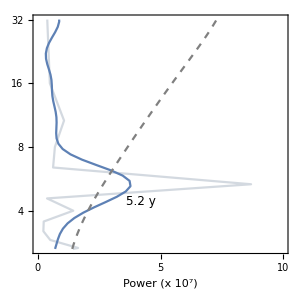
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
plotALL=Grid[{
{plotspdeaths},
{plotspectracomb,plotglobal}
},
Spacings->{-5,-5}
]
```